# Data Structures in the WaveletWare Package

Input for Computing and Plottingpaclet:WaveletWare/tutorial/Data Structures in the WaveletWare Package#452404853 | The Iteration Optionpaclet:WaveletWare/tutorial/Data Structures in the WaveletWare Package#472374342
Trees in WaveletWarepaclet:WaveletWare/tutorial/Data Structures in the WaveletWare Package#375198715 |

There are three special data structures used in the WaveletWare package.  Each are described in this tutorial.

This loads the package:

```mathematica
<<WaveletWare`
```

## Input for Computing and Plotting

(top)

Routines that compute (biorthogonal) wavelet (packet) transformations expect input data in one of the following formats:  a vector (list), a matrix or a list of three matrices each of which has the same dimensions.  

The function CheckDatapaclet:WaveletWare/ref/CheckData can be used (and is used internally by many WaveletWare functions) to determine if input data is in one of the correct formats.

CheckData | Determines format of data

Checking data format.

CheckDatapaclet:WaveletWare/ref/CheckData always returns a list of length 2.  The first number is 1,2,3,4 depending on if the input data is a vector, matrix, list of three matrices of equal dimensions, or none of the above.  The second value is the maximum number of iterations that can be performed on the input data.

```mathematica
v=7;
CheckData[v]

v="Hello";
CheckData[v]

v=Range[16];
CheckData[v]

v=ConstantArray[6,{12,15}];
CheckData[v]

t=ConstantArray[0,{8,8}];
v=ConstantArray[t,3];
CheckData[v]
```

{4,0}

{4,0}

{1,4}

{2,0}

{3,3}

## Trees in WaveletWare

(top)

A tree in the WaveletWare package is a structure that indicates a basis decomposition of a wavelet packet transformation.  Since a wavelet decomposition is a wavelet packet decomposition, a tree can be defined for a wavelet transform as well.

All values in a tree are either 0 or 1.  A 0/1 indicates that a certain portion of the transform is not/is part of the decomposition.

### One-Dimensional Data

(top of section)

Let's start with one-dimensional data and assume that k iterations of a full wavelet packet transformation are computed.  Then counting the original data, there are k+1 vectors in the output (with the original data counting as the 0th iteration).  At level k, the data are decomposed into 2^kblocks, each of equal length.  The cell below illustrates this process for k=0,1,2,3.

```mathematica
Map[ShowBestBasis[WaveletTree[#],ColorOn->White,ColorOff->White]&,Range[0,3]] // TableForm
```

-Graphics-

A tree is a list of length k+1 with 0 and 1 used to indicate which portions of the decomposition are not/are included in the best-basis representation.  The first element in the tree is either a 0 or 1.  Subsequent elements in the tree are lists of length 2,4,8,... and the values in any sublists are either 0 or 1.  

For example the wavelet decomposition for k=3 iterations is given below.

{0,{0,1},{0,1,0,0},{1,1,0,0,0,0,0,0}}

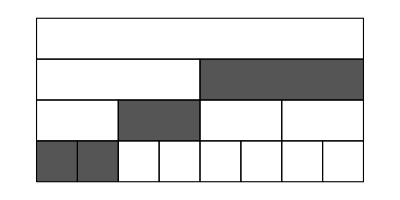

```mathematica
tree=WaveletTree[3]
ShowBestBasis[tree]
```

Trees cannot be comprised of arbitrary 0's and 1's.  A simple check of the validity is to start at the bottom level, partition it into groups of length 2, total each group and divide by 2.  Add this list to the next-to-last level and repeat.  When the process ends, the resulting value should be 1.

```mathematica
f[t_]:=Module[{p=Take[t,-2],q},
	q=First[p]+Map[Mean,Partition[Last[p],2]];
	Return[Append[Drop[t,-2],q]];
];
tree=WaveletTree[3];
Nest[f,tree,3]
```

{{1}}

The WaveletWare function CheckTreepaclet:WaveletWare/ref/CheckTree can be used to check the validity of a tree.  The input for this function is the tree and the datatype (1 since the tree was created from one-dimensional data).  If the tree is valid, CheckTreepaclet:WaveletWare/ref/CheckTree returns the number of iterations for the tree.

```mathematica
tree=WaveletTree[4];
CheckTree[tree,1]
```

4

In the cell below, the tree for the computed wavelet packet transform is displayed.

-Graphics-

{0,{0,0},{0,0,1,0},{1,1,1,1,0,0,1,1}}

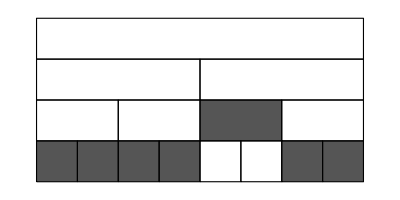

-Graphics-

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

{wt,tree}=WPT[v,SplineFilters[2,2],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->.1];
tree
ShowBestBasis[tree]
WaveletVectorPlot[wt,tree,NumIterations->3]
```

### Two-Dimensional Data

(top of section)

For two-dimensional data, the tree structure starts with a 0 or 1, but lists of length 2,4,8,... are replaced by matrices of dimension 2x2, 4x4, 8x8, ...

```mathematica
tree=WaveletTree[2,InputDimension->2]
ShowBestBasis[tree,Show3D->False]
```

{0,{{0,1},{1,1}},{{1,1,0,0},{1,1,0,0},{0,0,0,0},{0,0,0,0}}}

-Graphics-

The next cell illustrates the tree resulting from the wavelet packet transform.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

{wt,tree}=WPT[A,Daub[4],NumIterations->2,CostFunction->NumberAboveThreshold,SecondParameter->10];
tree
ShowBestBasis[tree,Show3D->False]
WaveletPlot[wt,tree,NumIterations->2]
```

-Graphics-

{0,{{0,0},{1,1}},{{1,1,1,1},{1,1,1,1},{0,0,0,0},{0,0,0,0}}}

-Graphics-

-Graphics-

## The Iteration Option

(top)

In visualization routines such as WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot, WaveletPlotpaclet:WaveletWare/ref/WaveletPlot, FullWaveletVectorPlotpaclet:WaveletWare/ref/FullWaveletVectorPlot and FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot, the Iterationpaclet:WaveletWare/ref/Iteration option can be set to indicate particular portions of the transformed data to be plotted.

### WaveletVectorPlot and FullWaveletVectorPlot

(top of section)

To view a particular region or regions of a wavelet transformation, the Iterationpaclet:WaveletWare/ref/Iteration option can be set.  In the case of WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot, the value for Iterationpaclet:WaveletWare/ref/Iteration is a list of lists each of length two.  If {i,j} is a particular list element, then i is the iteration for the region to be plotted and j=1,...,2^i.  Note that {i,j} must represent a valid portion of the transform data.

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

{wt,tree}=WPT[v,SplineFilters[2,2],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->.1];
ShowBestBasis[tree]
WaveletVectorPlot[wt,tree,NumIterations->3,ImageSize->300]

WaveletVectorPlot[wt,tree,NumIterations->3,Iteration->{{3,1},{3,2},{2,3}},ImageSize->300]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

FullWaveletVectorPlotpaclet:WaveletWare/ref/FullWaveletVectorPlot plots data generated by WTFullpaclet:WaveletWare/ref/WTFull or WPTFullpaclet:WaveletWare/ref/WPTFull.  The function WTFullpaclet:WaveletWare/ref/WTFull creates wavelet transforms for a prescribed number of iterations i (so each level is an iterated transform) and WPTFullpaclet:WaveletWare/ref/WPTFull generates a full decomposition at each level.  While regions in the output of WPTFullpaclet:WaveletWare/ref/WPTFull could be identified with lists of length 2, regions in the output of WTFullpaclet:WaveletWare/ref/WTFull need lists of length 3.  Thus for FullWaveletVectorPlotpaclet:WaveletWare/ref/FullWaveletVectorPlot, the Iterationpaclet:WaveletWare/ref/Iteration option value is a list of lists each of length three.

 If a particular list element is {i,j,k}, then i is the level of the output and {j,k} is the iteration and region as described for WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot.

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];

wtfull=WTFull[v,Haar[],NumIterations->3];
FullWaveletVectorPlot[wtfull] // TableForm

FullWaveletVectorPlot[wtfull,Iteration->{{0,0,1},{1,1,2},{3,3,1},{3,1,2}}] // TableForm
```

-Graphics-

-Graphics-

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];

wtfull=WTFull[v,Haar[],NumIterations->3];

FullWaveletVectorPlot[wtfull,PacketPlot->True,Iteration->{{1,1,2},{2,2,4},{3,3,1},{3,3,5}}] // TableForm
```

-Graphics-

### WaveletPlot and FullWaveletPlot

(top of section)

For matrix output plotted by WaveletPlotpaclet:WaveletWare/ref/WaveletPlot, the Iterationpaclet:WaveletWare/ref/Iteration option can be set to highlight only particular regions of the plot.  In this case the value of Iterationpaclet:WaveletWare/ref/Iteration is a list of lists of length 3.  If {i,j,k} is a list element, then i is the iteration of the region and then {j,k} represents the block location of the region.

```mathematica
f=PackageDirectory[DataType->Images]<>"car.png";
A=ImageRead[f,Resize->{128,192}];
ImagePlot[A]

wt=HWT[A,NumIterations->3];
WaveletPlot[wt,NumIterations->3]

WaveletPlot[wt,NumIterations->3,Iteration->{{1,2,2},{2,1,2},{3,1,1},{3,1,2}}]
```

-Graphics-

-Graphics-

-Graphics-

When FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot is used to plot output from WTFullpaclet:WaveletWare/ref/WTFull or WPTFullpaclet:WaveletWare/ref/WPTFull, the value for the Iteration option depends on the number of iterations that were computed of the transform.  If n iterations were computed, then the value of Iterationpaclet:WaveletWare/ref/Iteration is a list of length n+1.  Each list is then itself a list of ordered triples where the triples are described in the above section.  The value All can be used to plot all regions at a particular level and {} can be used to indicated no regions at the particular level are to be plotted.

```mathematica
file=PackageDirectory[DataType->Images]<>"tram.png";
A=ImageRead[file,Resize->{128,192}];
wt=WTFull[A,Haar[],NumIterations->2];
FullWaveletPlot[wt,Iteration->{All,All,{{2,1,1},{1,2,2}}}] // TableForm

FullWaveletPlot[wt,Iteration->{{},All,{{2,1,1},{2,1,2},{2,2,1},{2,2,2}}}] // TableForm
```

-Graphics-

-Graphics-

```mathematica
file=PackageDirectory[DataType->Images]<>"tram.png";
A=ImageRead[file,Resize->{128,192}];
wt=WPTFull[A,Haar[],NumIterations->2];
FullWaveletPlot[wt,Iteration->{{},{{1,1,1},{1,1,2}},{{2,2,2},{2,1,1}}}] // TableForm
```

-Graphics-

### WaveletPlot and FullWaveletPlot with Color Images

(top of section)

For color images with WaveletPlotpaclet:WaveletWare/ref/WaveletPlot, the value of Iterationpaclet:WaveletWare/ref/Iteration is a list of lists each of length 4.  If {c,i,j,k} is a list element, then c is the channel to be plotted and {i,j,k} is as described for a list value for Iteration when plotting matrices (see above).  In the case where the plotted data is from a wavelet transform or the regions in a packet transform are to all be plotted, the value All can be substituted for c.

```mathematica
file=PackageDirectory[DataType->Images]<>"fish.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

wt=HWT[A,NumIterations->2];
WaveletPlot[wt,NumIterations->2,Iteration->{{All,2,1,1},{1,1,1,2},{3,1,2,2}}]

WaveletPlot[wt,NumIterations->2,Iteration->{{All,2,1,1}},PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

For color images with FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot, the value of Iterationpaclet:WaveletWare/ref/Iteration depends on the number of iterations n of the transform that have been computed.  In this case, the value of Iterationpaclet:WaveletWare/ref/Iteration is a list of length n+1 and each element in this list is as described for color images and WaveletPlotpaclet:WaveletWare/ref/WaveletPlot in the above section.  All and {} can be used in lieu of a list item to plot all or none of the regions at a particular level.

```mathematica
file=PackageDirectory[DataType->Images]<>"cups.png";
A=ImageRead[file,Resize->{128,192}];
wt=WTFull[A,Haar[],NumIterations->2];
FullWaveletPlot[wt,Iteration->{All,{{All,1,1,1}},{{1,2,1,1},{2,2,1,2},{3,2,2,1}}}]

FullWaveletPlot[wt,Iteration->{All,{{All,1,1,1}},{{All,2,1,1}}},PlotTogether->True]
```

-Graphics-

-Graphics-